Ryan Foundoulis
605107291
ryanfoundoulis@gmail.com
HW 5

T = 1/2 m (r'[t]^2+r[t]^2 θ'[t]^2)

V = -4 m π^2 r[t]^(-1-ϵ)

Solution for ϵ = 0

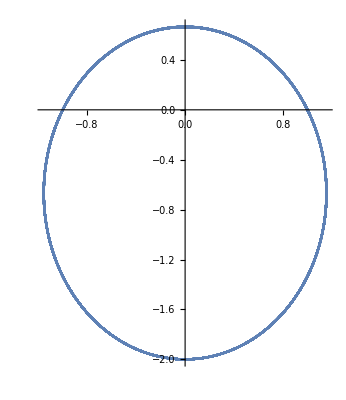

Solution for ϵ = 0.1

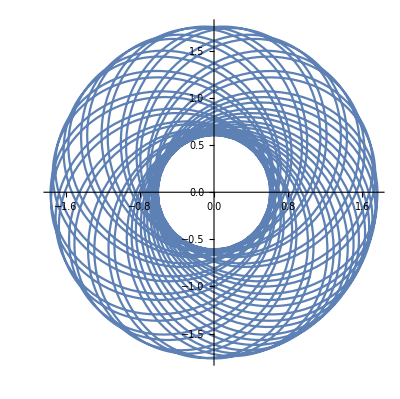

Solution for ϵ = -0.4

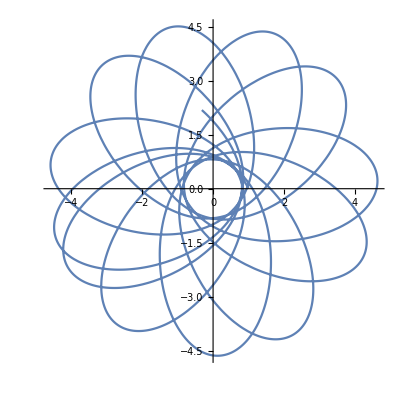

```mathematica
(* Problem 1 *)

Remove["Global`*"]

(* Defining lagrangian *)

T = 1/2 m (x'[t]^2+y'[t]^2);
V  = -4 π^2 m/r[t]^(1+ϵ);

lag = T-V;
EE = T + V;

(* Vector Coordinates of our reduced mass *)
x[t_] = r[t]Cos[θ[t]];
y[t_] = r[t]Sin[θ[t]];

(* Check *)

Print["\nT = ", T=T//Simplify]
Print["V = ", V= V //Simplify]

(* EL Operator *)

EL[q_] := D[lag, q] - Dt[D[lag,D[q,t]],t] == 0 //Simplify;

(* Cement EL Eq's *)

ellist = {EL[r[t]], EL[θ[t]]};

(* Prepare for NSolve *)

m = 1;
icList = {x[0] == 1, x'[0]== -π, y[0] ==0, y'[0] == 2π};
totList = Join[ellist,icList];

tlo = 0;
thi = 50;

(* Solution i *)

ϵ = 0;

solni = NDSolve[totList, {r,θ},{t,tlo,thi}, MaxSteps->50000][[1]];

Print["\n \n \nSolution for ϵ = 0"]

ParametricPlot[{x[t] /. solni, y[t] /. solni}, {t, tlo, thi}, AspectRatio->Automatic]

(* Solution ii *)

ϵ = 0.1;

solnii = NDSolve[totList, {r,θ},{t,tlo,thi}, MaxSteps->50000][[1]];

Print["Solution for ϵ = 0.1"]

ParametricPlot[{x[t] /. solnii, y[t] /. solnii}, {t, tlo, thi}, AspectRatio->Automatic]

(* Solution iii *)

ϵ = -0.4;

(* solniii = NDSolve[totList, {r,θ},{t,tlo,thi}, MaxSteps->50000][[1]] *)
(* This function about was used to generate the solution below, and then I use the solution below because it takes too long to recalculte in the program each time, any step count over 50,000 had my computer hang until I quit the kernel, no matter how long I waited*)

solniii = {r->InterpolatingFunction[…],θ->InterpolatingFunction[…]};

Print["Solution for ϵ = -0.4"]

ParametricPlot[{x[t] /. solniii, y[t] /. solniii}, {t, tlo, thi}, AspectRatio->Automatic]
```

```mathematica
(* Problem 2 *)
Remove["Global`*"]

(* Defining lagrangian *)

T = 1/2 m (x'[t]^2+y'[t]^2);
V  = -4 π^2 m/r[t]^(1+ϵ);

lag = T-V;
EE = T + V;

(* Vector Coordinates of our reduced mass *)
x[t_] = r[t]Cos[θ[t]];
y[t_] = r[t]Sin[θ[t]];

(* Check *)

Print["\nT = ", T=T//Simplify]
Print["V = ", V= V //Simplify]

(* EL Operator *)

EL[q_] := D[lag, q] - Dt[D[lag,D[q,t]],t] == 0 //Simplify;

(* Cement EL Eq's *)

ellist = {EL[r[t]], EL[θ[t]]};

(* Prepare for NSolve *)

m = 1;
icList = {x[0] == 1, x'[0]== -π, y[0] ==0, y'[0] == 2π};
totList = Join[ellist,icList];

tlo = 0;
thi = 50;

(* Solution i *)

ϵ = 0;

solni = NDSolve[totList, {r,θ},{t,tlo,thi}, MaxSteps->50000][[1]];

Print["\n \n \nSolution for ϵ = 0"]

sun = Graphics[{Yellow, PointSize[0.07],Point[{0,0}]}];
orbit1[t_] := Graphics[{Cyan, PointSize[0.05],Point[{x[t]/.solni,y[t]/.solni}]}]
Line1[t_] :=Graphics[{LightBlue, Line[{{0,0},{x[t]/.solni,y[t]/.solni}}]}]
traj[t_]:=ParametricPlot[{x[t],y[t]} /. solni, {t,tlo,thi}];
art[t_]=Show[traj[t],sun, orbit1[t], Line1[t],PlotRange-> {{-1.21,1.21},{-2.5,1}}, AxesLabel->{x,y}];
Animate[art[t], {t, tlo, thi}]



(* Solution ii *)

ϵ = 0.1;

solnii = NDSolve[totList, {r,θ},{t,tlo,thi}, MaxSteps->50000][[1]];

Print["Solution for ϵ = 0.1"]

(* ParametricPlot[{x[t] /. solnii, y[t] /. solnii}, {t, tlo, thi}, AspectRatio->Automatic]*)

sun2 = Graphics[{Yellow, PointSize[0.07],Point[{0,0}]}];
orbit2[t_] := Graphics[{Cyan, PointSize[0.05],Point[{x[t]/.solnii,y[t]/.solnii}]}]
Line2[t_] :=Graphics[{LightBlue, Line[{{0,0},{x[t]/.solnii,y[t]/.solnii}}]}]
traj2[t_]:=ParametricPlot[{x[t],y[t]} /. solnii, {t,tlo,thi}];
art2[t_]=Show[traj2[t],sun2, orbit2[t], Line2[t],PlotRange-> {{-2,2},{-2,2}}, AxesLabel->{x,y}];
Animate[art2[t], {t, tlo, thi}]

(* Solution iii *)

ϵ = -0.4;

(* solniii = NDSolve[totList, {r,θ},{t,tlo,thi}, MaxSteps->50000][[1]] *)
(* This function about was used to generate the solution below, and then I use the solution below because it takes too long to recalculte in the program each time, any step count over 50,000 had my computer hang until I quit the kernel, no matter how long I waited*)

solniii = {r->InterpolatingFunction[…],θ->InterpolatingFunction[…]};

Print["Solution for ϵ = -0.4"]

(*ParametricPlot[{x[t] /. solniii, y[t] /. solniii}, {t, tlo, thi}, AspectRatio->Automatic]*)

sun3 = Graphics[{Yellow, PointSize[0.07],Point[{0,0}]}];
orbit3[t_] := Graphics[{Cyan, PointSize[0.05],Point[{x[t]/.solniii,y[t]/.solniii}]}]
Line3[t_] :=Graphics[{LightBlue, Line[{{0,0},{x[t]/.solniii,y[t]/.solniii}}]}]
traj3[t_]:=ParametricPlot[{x[t],y[t]} /. solniii, {t,tlo,thi}];
art3[t_]=Show[traj3[t],sun3, orbit3[t], Line3[t], AxesLabel->{x,y},PlotRange-> {{-5,5},{-5,5}}];
Animate[art3[t], {t, tlo, thi}]
```

T = 1/2 m (r'[t]^2+r[t]^2 θ'[t]^2)

V = -4 m π^2 r[t]^(-1-ϵ)

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Solution for ϵ = 0

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Solution for ϵ = 0.1

Solution for ϵ = -0.4

```mathematica
(* Problem 3 *)

T = 1/2 m1(x1'[t]^2+y1'[t]^2)+ 1/2 m2(x2'[t]^2+y2'[t]^2);
V  = -G m1 m2/r[t];

lag = T-V;
EE = T + V;

(* Vector Coordinates of our reduced mass *)
r[t_] = √((x2[t]-x1[t])^2+(y2[t]-y1[t])^2);

(* Check *)

Print["\nT = ", T=T//Simplify]
Print["V = ", V= V //Simplify]

(* EL Operator *)

EL[q_] := D[lag, q] - Dt[D[lag,D[q,t]],t] == 0 //Simplify;

ellist = {EL[x1[t]],EL[y1[t]],EL[x2[t]],EL[y2[t]]};

(* Prepare for NSolve *)

m1 = 10;
m2 = 15;
G = 1;
icList = {x1[0] == 0, x1'[0]== 1, y1[0] ==10, y1'[0] == 0,x2[0] == 0, x2'[0]== 0, y2[0] ==0, y2'[0] == 0};
totList = Join[ellist,icList];

tlo = 0;
thi = 100;

(* Solution i *)

soln = NDSolve[totList, {x1,y1,x2,y2},{t,tlo,thi}, MaxSteps->50000][[1]];

xCoM[t_] = (m1 x1[t]+m2 x2[t])/(m1 + m2);
yCoM[t_] = (m1 y1[t]+m2 y2[t])/(m1 + m2);


orbit1[t_] := Graphics[{White, PointSize[0.03],Point[{x1[t]/.soln,y1[t]/.soln}]}]
orbit2[t_] := Graphics[{White, PointSize[0.03],Point[{x2[t]/.soln,y2[t]/.soln}]}]
orbit3[t_] := Graphics[{Black, PointSize[0.02],Point[{xCoM[t]/.soln,yCoM[t]/.soln}]}]

traj1[t_]:=ParametricPlot[{x1[t],y1[t]} /. soln, {t,tlo,thi},PlotStyle->Orange] ;
traj2[t_]:=ParametricPlot[{x2[t],y2[t]} /. soln, {t,tlo,thi}];
traj3[t_] :=ParametricPlot[{xCoM[t],yCoM[t]} /. soln, {t, tlo, thi}, PlotStyle->Dashed];


art4[t_]=Show[traj1[t],traj2[t], traj3[t], orbit1[t], orbit2[t], orbit3[t], PlotRange-> {{-0,40},{0,15}}, AxesLabel->{x,y}];
Animate[art4[t], {t, tlo, thi}]

(* Movement in CoM Frame *)

x1New[t_] = (x1[t]-xCoM[t])/.soln;
y1New[t_] = (y1[t]-yCoM[t])/.soln;

x2New[t_] = (x2[t]-xCoM[t])/.soln;
y2New[t_] = (y2[t]-yCoM[t])/.soln;

sun4 = Graphics[{Black, PointSize[0.03],Point[{0,0}]}];
orbit1N[t_] := Graphics[{White, PointSize[0.03],Point[{x1New[t],y1New[t]}]}]
orbit2N[t_] := Graphics[{White, PointSize[0.03],Point[{x2New[t],y2New[t]}]}]

traj1N[t_]:=ParametricPlot[{x1New[t],y1New[t]}, {t,tlo,thi},PlotStyle->Orange, Axes->True, AxesLabel->{x,y}];
traj2N[t_]:=ParametricPlot[{x2New[t],y2New[t]}, {t,tlo,thi}, Axes->True, AxesLabel->{x,y}];

art5[t_] = Show[ traj1N[t],traj2N[t], orbit1N[t], orbit2N[t],sun4, PlotRange-> {{-10,10},{-10,10}}];
Animate[art5[t], {t, tlo, thi}]
```

T = 1/2 (m1 (x1'[t]^2+y1'[t]^2)+m2 (x2'[t]^2+y2'[t]^2))

V = -(G m1 m2)/(√((x1[t]-x2[t])^2+(y1[t]-y2[t])^2))